```mathematica
npair2[i_]:={i-Floor[(-1+Sqrt[8*i-7])/2]*(Floor[(-1+Sqrt[8*i-7])/2]+1)/2 ,Floor[3/2+Sqrt[2*i-2]]}
npair[i_]:={npair2[i][[1]],npair2[i+1][[2]]}
npairnum[{i_,j_}]:=If[i<j,1+i+1/2 (-3+j) j,-(1+j+1/2 (-3+i) i)]
Table[npairnum[Reverse[npair[i]]],{i,1,10}]
```

{-1,-2,-3,-4,-5,-6,-7,-8,-9,-10}

```mathematica
tolist[l_]:=Table[l[[i]],{i,1,Length[l]}]
```

```mathematica
SumGeqM[l_,m_]:=BooleanMinimize[Block[{ss=Subsets[l,{m}]},Or@@Table[And@@ss[[i]],{i,1,Length[ss]}]],"CNF"]
SumGeqM[{1,2,3,4,5,6,7,8,9,10,11},2]
tolist[%]//Column
```

(1||2||3||4||5||6||7||8||9||10)&&(1||2||3||4||5||6||7||8||9||11)&&(1||2||3||4||5||6||7||8||10||11)&&(1||2||3||4||5||6||7||9||10||11)&&(1||2||3||4||5||6||8||9||10||11)&&(1||2||3||4||5||7||8||9||10||11)&&(1||2||3||4||6||7||8||9||10||11)&&(1||2||3||5||6||7||8||9||10||11)&&(1||2||4||5||6||7||8||9||10||11)&&(1||3||4||5||6||7||8||9||10||11)&&(2||3||4||5||6||7||8||9||10||11)

1||2||3||4||5||6||7||8||9||10
1||2||3||4||5||6||7||8||9||11
1||2||3||4||5||6||7||8||10||11
1||2||3||4||5||6||7||9||10||11
1||2||3||4||5||6||8||9||10||11
1||2||3||4||5||7||8||9||10||11
1||2||3||4||6||7||8||9||10||11
1||2||3||5||6||7||8||9||10||11
1||2||4||5||6||7||8||9||10||11
1||3||4||5||6||7||8||9||10||11
2||3||4||5||6||7||8||9||10||11

```mathematica
!Subscript[y, 2]/.{Subscript[p_,q_]->q}/.{!p_->-p}
```

-2

```mathematica
Clear[x,y]
```

```mathematica
n
```

4

```mathematica
BooleanMinimize[!(!a&&!b&&!c)]
```

a||b||c

```mathematica
Partition[Table[Subscript[x, i],{i,1,2n}],n]
```

{{x_1,x_2,x_3,x_4},{x_5,x_6,x_7,x_8}}

```mathematica
tolist[BooleanConvert[((x12&&i12o1&&i12o2&&i12o3)||(x21&&i21o1&&i21o2&&i21o3)||(!x12&&!x21))&&(x13&&i13o1&&i13o2&&i13o3)||(x31&&i31o1&&i31o2&&i31o3)||(!x13&&!x31),"CNF"]]//Column
```

```mathematica
({1,2}&&INEQ[1,2]||{2,1}&&INEQ[2,1]||!{1,2}&&!{2,1})&&({1,3}&&INEQ[1,3]||{3,1}&&INEQ[3,1]||True)&&
```

```mathematica
"
|a_i's| == |b_i's| == L
a_(i + L) := b_i

∑a_i≥∑¬b_i+2==∧_(t ∈ T)(∨t)

Where T is the set of increasing tuples of length L with elements from [1,2 L].
";


"
S_i is the set of variables for the ith path

|S_i's| == L
∀ t  (t strictly increasing and |t| == L) ⇒ (c[t[1]] ∨ c[t[2]] ∨ c[t[3]] ∨ ...)
c_x := Piecewise[{{∧S_x, x≤ L}, {∨S_(x-L), x>L}}]



∨{c_i,c_j,c_k,c_l} : i<j<k<l
(c_x : x ≤ len) := ∧ S_x
(c_x : x > len) := ∨ S_(x - len)

a_1 :=   ∧ S_1
b_1 := ¬(∨ S_1)
S_1 := {α_1,α_2,α_3}

a_1 := α_1∧α_2∧α_3
b_1 := ¬(α_1∨α_2∨α_3)
";


"
a := α_1∧α_2∧α_3
b := !α_1∧!α_2∧!α_3
!b := !(!α_1∧!α_2∧!α_3)
!b := α_1∨α_2∨α_3
b := ¬(α_1∨α_2∨α_3)
";
```

```mathematica
BooleanConvert[(a1&&a2&&a3)||(b1&&b2&&b3)||c1||c2||c3,"CNF"]
```

(a1||b1||c1||c2||c3)&&(a1||b2||c1||c2||c3)&&(a1||b3||c1||c2||c3)&&(a2||b1||c1||c2||c3)&&(a2||b2||c1||c2||c3)&&(a2||b3||c1||c2||c3)&&(a3||b1||c1||c2||c3)&&(a3||b2||c1||c2||c3)&&(a3||b3||c1||c2||c3)

```mathematica
n=3
GtEqCNFPlus2[x_,y_]:=Block[{xlen=Length[x],ylen=Length[y]},
And@@Table[((SumGeqM[y,i])⇒SumGeqM[x,i+1]),{i,0,xlen-1}]]
GtEqCNFPlus2@@Partition[Join[Table[Subscript[x, i],{i,1,n}],Table[!Subscript[x, i],{i,n+1,2n}]],n]
Column[tolist[%]]
tolist[Map[tolist[#]/.{Subscript[x,q_]->q}/.{!p_->-p}&,GtEqCNFPlus2@@Partition[Join[Table[Subscript[x, i],{i,1,n}],Table[!Subscript[x, i],{i,n+1,2n}]],n]]]//Column
```

3

(x_1||x_2||x_3)&&(!x_4||!x_5||!x_6⇒(x_1||x_2)&&(x_1||x_3)&&(x_2||x_3))&&((!x_4||!x_5)&&(!x_4||!x_6)&&(!x_5||!x_6)⇒x_1&&x_2&&x_3)

x_1||x_2||x_3
!x_4||!x_5||!x_6⇒(x_1||x_2)&&(x_1||x_3)&&(x_2||x_3)
(!x_4||!x_5)&&(!x_4||!x_6)&&(!x_5||!x_6)⇒x_1&&x_2&&x_3

{1,2,3}
{-4||-5||-6,(1||2)&&(1||3)&&(2||3)}
{(-4||-5)&&(-4||-6)&&(-5||-6),1&&2&&3}

```mathematica
∑_(i=1)^L Subscript[x, i]<∑_(i=L+1)^(2L) ¬Subscript[x, i]

0≤∑_(i=1)^L Subscript[x, i]⇒1≤∑_(i=L+1)^(2L) ¬Subscript[x, i]
1≤∑_(i=1)^L Subscript[x, i]⇒2≤∑_(i=L+1)^(2L) ¬Subscript[x, i]
2≤∑_(i=1)^L Subscript[x, i]⇒3≤∑_(i=L+1)^(2L) ¬Subscript[x, i]

m+0≤∑_(i=1)^L Subscript[x, i]=∨((m+0)-tuples∧-ed)
m+1≤∑_(i=1)^L ¬Subscript[x, i]=∨((m+1)-tuples ∧¬-ed)

!((1&&2)||(1&&3)||(2&&3))||((!4&&!5)||(!4&&!6)||(!5&&!6))
(!(1&&2)&&!(1&&3)&&!(2&&3))||((!4&&!5)||(!4&&!6)||(!5&&!6))
((!1||!2)&&(!1||!3)&&(!2||!3))||((!4&&!5)||(!4&&!6)||(!5&&!6))
((!1||!2)&&(!1||!3)&&(!2||!3))||(!4&&!5)||(!4&&!6)||(!5&&!6)

!1||!2||(!4&&!5)||(!4&&!6)||(!5&&!6)->!1||!2||(!4&&!5)||(!4&&!6)||(!5&&!6)
!1||!3||(!4&&!5)||(!4&&!6)||(!5&&!6)-> w
!2||!3||(!4&&!5)||(!4&&!6)||(!5&&!6)->w


((!1||!2)&&(!1||!3)&&(!2||!3))||((!4&&!5)||(!4&&!6)||(!5&&!6))
((!1||L1)&&  L2)                                             ||((!4&&L3)||L4)

(!1||!4||L1||L4)&&(!1||L1||L3||L4)&&(!4||L2||L4)&&(L2||L3||L4)


(!1||!4||L1||L4)&&(!1||L1||L3||L4)&&(!4||L2||L4)&&(L2||L3||L4)
L1->!2||M1
L2->(!3||!3)&&M2
L3->!5&&M3
L4->(!4&&!6)||M4
```

```mathematica
BooleanMinimize[((!1||!L1)&&!L2)||((!4&&!L3)||!L4),"CNF"]
```

(!1||!4||!L1||!L4)&&(!1||!L1||!L3||!L4)&&(!4||!L2||!L4)&&(!L2||!L3||!L4)

```mathematica
"This shows than an implication cycle means everything in the cycle is equal";
BooleanMinimize[(a⇒b)&&(b⇒c)&&(c⇒d)&&(d⇒a),"DNF"]
```

(a&&b&&c&&d)||(!a&&!b&&!c&&!d)

```mathematica
BooleanConvert[!((1&&2)||(1&&3)||(2&&3))||((!4&&!5)||(!4&&!6)||(!5&&!6)),"DNF"]
```

(!1&&!2)||(!1&&!3)||(!2&&!3)||(!4&&!5)||(!4&&!6)||(!5&&!6)

```mathematica
1+2+3<!4+!5+!6;
BooleanConvert[((!4||!5||!6))&&((1||2||3)⇒((!4&&!5)||(!4&&!6)||(!5&&!6)))&&(((1&&2)||(1&&3)||(2&&3))⇒(!4&&!5&&!6)),"CNF"]
```

(!1||!2||!4)&&(!1||!2||!5)&&(!1||!2||!6)&&(!1||!3||!4)&&(!1||!3||!5)&&(!1||!3||!6)&&(!1||!4||!5)&&(!1||!4||!6)&&(!1||!5||!6)&&(!2||!3||!4)&&(!2||!3||!5)&&(!2||!3||!6)&&(!2||!4||!5)&&(!2||!4||!6)&&(!2||!5||!6)&&(!3||!4||!5)&&(!3||!4||!6)&&(!3||!5||!6)&&(!4||!5||!6)

```mathematica
1+2+3+4<5+6+7+8
```

```mathematica
True                        ⇒(5||6||7||8)
(1||2||3||4)⇒((5&&6)||(5&&7)||(5&&8)||(6&&7)||(6&&8)||(7&&8))
((1&&2)||(1&&3)||(1&&4)||(2&&3)||(2&&4)||(3&&4))⇒((5&&6&&7)||(5&&6&&8)||(6&&7&&8))
((1&&2&&3)||(1&&2&&4)||(2&&3&&4))⇒(5&&6&&7&&8)
(1&&2&&3&&4)⇒False

(5&&6&&7&&8)⇒(!1||!2||!3||!4)
(!5||!6||!7||!8)⇒((!1&&!2)||(!1&&!3)||(!1&&!4)||(!2&&!3)||(!3&&!4))
((!5&&!6)||(!5&&!7)||(!5&&!8)||(!6&&!7)||(!6&&!8)||(!7&&!8))⇒((!1&&!2&&!3)||(!1&&!2&&!4)||(!2&&!3&&!4))
((!5&&!6&&!7)||(!5&&!6&&!8)||(!6&&!7&&!8))⇒(!1&&!2&&!3&&!4)
(!5&&!6&&!7&&!8)⇒False
```

```mathematica
BooleanConvert[True                        ⇒(5||6||7||8),"CNF"]
BooleanConvert[(1||2||3||4)⇒((5&&6)||(5&&7)||(5&&8)||(6&&7)||(6&&8)||(7&&8)),"CNF"]
BooleanConvert[((1&&2)||(1&&3)||(1&&4)||(2&&3)||(2&&4)||(3&&4))⇒((5&&6&&7)||(5&&6&&8)||(6&&7&&8)),"CNF"]
BooleanConvert[((1&&2&&3)||(1&&2&&4)||(2&&3&&4))⇒(5&&6&&7&&8),"CNF"]
BooleanConvert[(1&&2&&3&&4)⇒False,"CNF"]
"hi"
BooleanConvert[(5&&6&&7&&8)⇒(!1||!2||!3||!4),"CNF"]
BooleanConvert[(!5||!6||!7||!8)⇒((!1&&!2)||(!1&&!3)||(!1&&!4)||(!2&&!3)||(!3&&!4)),"CNF"]
BooleanConvert[((!5&&!6)||(!5&&!7)||(!5&&!8)||(!6&&!7)||(!6&&!8)||(!7&&!8))⇒((!1&&!2&&!3)||(!1&&!2&&!4)||(!2&&!3&&!4)),"CNF"]
BooleanConvert[((!5&&!6&&!7)||(!5&&!6&&!8)||(!6&&!7&&!8))⇒(!1&&!2&&!3&&!4),"CNF"]
BooleanConvert[(!5&&!6&&!7&&!8)⇒False,"CNF"]
```

5||6||7||8

(!1||5||6||7)&&(!1||5||6||8)&&(!1||5||7||8)&&(!1||6||7||8)&&(!2||5||6||7)&&(!2||5||6||8)&&(!2||5||7||8)&&(!2||6||7||8)&&(!3||5||6||7)&&(!3||5||6||8)&&(!3||5||7||8)&&(!3||6||7||8)&&(!4||5||6||7)&&(!4||5||6||8)&&(!4||5||7||8)&&(!4||6||7||8)

(!1||!2||5||7)&&(!1||!2||5||8)&&(!1||!2||6)&&(!1||!2||7||8)&&(!1||!3||5||7)&&(!1||!3||5||8)&&(!1||!3||6)&&(!1||!3||7||8)&&(!1||!4||5||7)&&(!1||!4||5||8)&&(!1||!4||6)&&(!1||!4||7||8)&&(!2||!3||5||7)&&(!2||!3||5||8)&&(!2||!3||6)&&(!2||!3||7||8)&&(!2||!4||5||7)&&(!2||!4||5||8)&&(!2||!4||6)&&(!2||!4||7||8)&&(!3||!4||5||7)&&(!3||!4||5||8)&&(!3||!4||6)&&(!3||!4||7||8)

(!1||!2||!3||5)&&(!1||!2||!3||6)&&(!1||!2||!3||7)&&(!1||!2||!3||8)&&(!1||!2||!4||5)&&(!1||!2||!4||6)&&(!1||!2||!4||7)&&(!1||!2||!4||8)&&(!2||!3||!4||5)&&(!2||!3||!4||6)&&(!2||!3||!4||7)&&(!2||!3||!4||8)

!1||!2||!3||!4

hi

!1||!2||!3||!4||!5||!6||!7||!8

(!1||!2||!4||5)&&(!1||!2||!4||6)&&(!1||!2||!4||7)&&(!1||!2||!4||8)&&(!1||!3||5)&&(!1||!3||6)&&(!1||!3||7)&&(!1||!3||8)&&(!2||!3||!4||5)&&(!2||!3||!4||6)&&(!2||!3||!4||7)&&(!2||!3||!4||8)

(!1||!3||5||6)&&(!1||!3||5||7)&&(!1||!3||5||8)&&(!1||!3||6||7)&&(!1||!3||6||8)&&(!1||!3||7||8)&&(!1||!4||5||6)&&(!1||!4||5||7)&&(!1||!4||5||8)&&(!1||!4||6||7)&&(!1||!4||6||8)&&(!1||!4||7||8)&&(!2||5||6)&&(!2||5||7)&&(!2||5||8)&&(!2||6||7)&&(!2||6||8)&&(!2||7||8)&&(!3||!4||5||6)&&(!3||!4||5||7)&&(!3||!4||5||8)&&(!3||!4||6||7)&&(!3||!4||6||8)&&(!3||!4||7||8)

(!1||5||6||7)&&(!1||5||6||8)&&(!1||6||7||8)&&(!2||5||6||7)&&(!2||5||6||8)&&(!2||6||7||8)&&(!3||5||6||7)&&(!3||5||6||8)&&(!3||6||7||8)&&(!4||5||6||7)&&(!4||5||6||8)&&(!4||6||7||8)

5||6||7||8

```mathematica
BooleanConvert[((!4&&!5&&!6)⇒(!1||!2||!3))&&((!!4||!!5||!!6)⇒(!(1&&2)||!(1&&3)||!(2&&3)))&&((!(!4&&!5)||!(!4&&!6)||!(!5&&!6))⇒!(1||2||3)),"CNF"]
```

(!1||!2||!3)&&(!1||!4)&&(!1||!5)&&(!1||!6)&&(!2||!4)&&(!2||!5)&&(!2||!6)&&(!3||!4)&&(!3||!5)&&(!3||!6)

```mathematica
BooleanConvert[((!1||!2||!4)&&(!1||!2||!5)&&(!1||!2||!6)&&(!1||!3||!4)&&(!1||!3||!5)&&(!1||!3||!6)&&(!1||!4||!5)&&(!1||!4||!6)&&(!1||!5||!6)&&(!2||!3||!4)&&(!2||!3||!5)&&(!2||!3||!6)&&(!2||!4||!5)&&(!2||!4||!6)&&(!2||!5||!6)&&(!3||!4||!5)&&(!3||!4||!6)&&(!3||!5||!6)&&(!4||!5||!6))&&((!1||!2||!3)&&(!1||!4)&&(!1||!5)&&(!1||!6)&&(!2||!4)&&(!2||!5)&&(!2||!6)&&(!3||!4)&&(!3||!5)&&(!3||!6)),"CNF"]
```

(!1||!2||!3)&&(!1||!4)&&(!1||!5)&&(!1||!6)&&(!2||!4)&&(!2||!5)&&(!2||!6)&&(!3||!4)&&(!3||!5)&&(!3||!6)&&(!4||!5||!6)

```mathematica
BooleanConvert[(!4&&L3)||L4,"CNF"]
```

(!4||L4)&&(L3||L4)

```mathematica
BooleanConvert[(a||b)||(c&&d),"CNF"]
```

(a||b||c)&&(a||b||d)

```mathematica
BooleanConvert[(a&&b&&c)||d||e||f,"CNF"]
```

(a||d||e||f)&&(b||d||e||f)&&(c||d||e||f)

```mathematica
BooleanConvert[(¬Subscript[s, 1]∧¬Subscript[s, 2]∧¬Subscript[s, 3])||¬Subscript[t, 1]∨¬Subscript[t, 2]∨¬Subscript[t, 3],"CNF"]
```

(!s_1||!t_1||!t_2||!t_3)&&(!s_2||!t_1||!t_2||!t_3)&&(!s_3||!t_1||!t_2||!t_3)

```mathematica
BooleanConvert[b||(c&&d),"CNF"]
```

(b||c)&&(b||d)

```mathematica
Simplify[Reduce[(a+1≤b)&&(a<b)],a+1≤b]
```

True

```mathematica
Or@@Map[Fold[And,True,#]&,Subsets[{1,2,3,4},{2}]]
```

(1&&2)||(1&&3)||(1&&4)||(2&&3)||(2&&4)||(3&&4)

```mathematica
Or@@Map[Fold[And,True,Map[!#&,#]]&,Subsets[{1,2,3,4,5},{4}]]
```

(!1&&!2&&!3&&!4)||(!1&&!2&&!3&&!5)||(!1&&!2&&!4&&!5)||(!1&&!3&&!4&&!5)||(!2&&!3&&!4&&!5)

```mathematica
atleast[l_,n_]:=If[n==0,True,Or@@Map[Fold[And,True,#]&,Subsets[l,{n}]]]
atleast[{1,2,3,4},2]
BooleanMinimize[%,"CNF"]
Table[BooleanMinimize[atleast[Range[1,i],i-1],"CNF"],{i,1,5}]//Column
```

(1&&2)||(1&&3)||(1&&4)||(2&&3)||(2&&4)||(3&&4)

(1||2||3)&&(1||2||4)&&(1||3||4)&&(2||3||4)

True
1||2
(1||2)&&(1||3)&&(2||3)
(1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4)
(1||2)&&(1||3)&&(1||4)&&(1||5)&&(2||3)&&(2||4)&&(2||5)&&(3||4)&&(3||5)&&(4||5)

```mathematica
"n ≤ l ≡ ∀ s∈S, ∃ e∈s, e is True
 S := {s ⊆ S : |s| == n}
" 
"l ≤ |l| - n ≡ ∀ s∈S, ∃ e∈S, e is False"
```

```mathematica
!(n≤X)||(n≤Y)
!(∀ s∈Subscript[S, n], ∃ e∈s, e is True)||(∀ t∈Subscript[T, n], ∃ f∈t, f is True)
!(∀ s∈Subscript[S, n], ∃ e∈s, e is False)||(∀ t∈Subscript[T, n], ∃ f∈s, f is False)
(∃ s∈Subscript[S, n], ∀ e∈s, !e)||(∀ t∈Subscript[T, n], ∃ f∈t, f)
(∃ s∈Subscript[S, n], ∀ e∈s, e)||(∀ t∈Subscript[T, n], ∃ f∈s, f is False)
```

```mathematica
BooleanConvert[a⧦b,"CNF"]
```

(!a||b)&&(a||!b)

```mathematica
(!(a<b)||(((b≤n)⇒(a≤n-1))&&((a≥m)⇒(b≥m+1))))&&((a<b)||!(((b≤n)⇒(a≤n-1))&&((a≥m)⇒(b≥m+1))))
(!(a<b)||((!(b≤n)||(a≤n-1))&&(!(a≥m)||(b≥m+1))))&&((a<b)||!((!(b≤n)||(a≤n-1))&&(!(a≥m)||(b≥m+1))))
((a≥b)||(((b>n)||(a≤n-1))&&((a<m)||(b≥m+1))))&&((a<b)||(!((b>n)||(a≤n-1))||!((a<m)||(b≥m+1))))
((a≥b)||(((b>n)||(a≤n-1))&&((a<m)||(b≥m+1))))&&((a<b)||((!(b>n)&&!(a≤n-1))||(!(a<m)&&!(b≥m+1))))
((a≥b)||(((b>n)||(a≤n-1))&&((a<m)||(b≥m+1))))&&((a<b)||(((b≤n)&&(a>n-1))||((a≥m)&&(b<m+1))))
```

```mathematica
BooleanConvert[((a≥b)||(((b>n)||(a≤n-1))&&((a<m)||(b≥m+1))))&&((a<b)||(((b≤n)&&(a>n-1))||((a≥m)&&(b<m+1)))),"DNF"]
```

(a<b&&a<m&&a≤-1+n)||(a<b&&a<m&&b>n)||(a<b&&b≥1+m&&a≤-1+n)||(a<b&&b≥1+m&&b>n)||(a≥b&&a≥m&&b<1+m)||(a≥b&&a>-1+n&&b≤n)

```mathematica
Reduce[{a≥0,b≥0,(a<b)&&!ForAll[n,1≤n,ForAll[m,0≤m,(((b≤n)⇒(a≤n-1))&&((a≥m)⇒(b≥m+1)))]]},Integers]
```

False

```mathematica
Reduce[{a≥0,b≥0,!(a<b)&&ForAll[n,1≤n,ForAll[m,0≤m,(((b≤n)⇒(a≤n-1))&&((a≥m)⇒(b≥m+1)))]]},Integers]
```

False

```mathematica
BooleanConvert[!(a⧦b),"DNF"]
```

(a&&!b)||(!a&&b)

```mathematica
n=4;
atmost[Range[n+1,2n],2]⇒atmost[Map[!#&,Range[1,n]],1]
BooleanConvert[%,"CNF"]
atleast[Map[!#&,Range[1,n]],2]⇒atleast[Range[n+1,2n],3]
BooleanConvert[%,"CNF"]
```

(!5&&!6)||(!5&&!7)||(!5&&!8)||(!6&&!7)||(!6&&!8)||(!7&&!8)⇒(1&&2&&3)||(1&&2&&4)||(1&&3&&4)||(2&&3&&4)

(1||2||5||6)&&(1||2||5||7)&&(1||2||5||8)&&(1||2||6||7)&&(1||2||6||8)&&(1||2||7||8)&&(1||3||5||6)&&(1||3||5||7)&&(1||3||5||8)&&(1||3||6||7)&&(1||3||6||8)&&(1||3||7||8)&&(1||4||5||6)&&(1||4||5||7)&&(1||4||5||8)&&(1||4||6||7)&&(1||4||6||8)&&(1||4||7||8)&&(2||3||5||6)&&(2||3||5||7)&&(2||3||5||8)&&(2||3||6||7)&&(2||3||6||8)&&(2||3||7||8)&&(2||4||5||6)&&(2||4||5||7)&&(2||4||5||8)&&(2||4||6||7)&&(2||4||6||8)&&(2||4||7||8)&&(3||4||5||6)&&(3||4||5||7)&&(3||4||5||8)&&(3||4||6||7)&&(3||4||6||8)&&(3||4||7||8)

(!1&&!2)||(!1&&!3)||(!1&&!4)||(!2&&!3)||(!2&&!4)||(!3&&!4)⇒(5&&6&&7)||(5&&6&&8)||(5&&7&&8)||(6&&7&&8)

(1||2||5||6)&&(1||2||5||7)&&(1||2||5||8)&&(1||2||6||7)&&(1||2||6||8)&&(1||2||7||8)&&(1||3||5||6)&&(1||3||5||7)&&(1||3||5||8)&&(1||3||6||7)&&(1||3||6||8)&&(1||3||7||8)&&(1||4||5||6)&&(1||4||5||7)&&(1||4||5||8)&&(1||4||6||7)&&(1||4||6||8)&&(1||4||7||8)&&(2||3||5||6)&&(2||3||5||7)&&(2||3||5||8)&&(2||3||6||7)&&(2||3||6||8)&&(2||3||7||8)&&(2||4||5||6)&&(2||4||5||7)&&(2||4||5||8)&&(2||4||6||7)&&(2||4||6||8)&&(2||4||7||8)&&(3||4||5||6)&&(3||4||5||7)&&(3||4||5||8)&&(3||4||6||7)&&(3||4||6||8)&&(3||4||7||8)

```mathematica
(!1&&!2)||(!1&&!3)||(!1&&!4)||(!2&&!3)||(!2&&!4)||(!3&&!4)⇒(5&&6&&7)||(5&&6&&8)||(5&&7&&8)||(6&&7&&8);
!((!1&&!2)||(!1&&!3)||(!1&&!4)||(!2&&!3)||(!2&&!4)||(!3&&!4))||(5&&6&&7)||(5&&6&&8)||(5&&7&&8)||(6&&7&&8);
(!(!1&&!2)&&!(!1&&!3)&&!(!1&&!4)&&!(!2&&!3)&&!(!2&&!4)&&!(!3&&!4))||(5&&6&&7)||(5&&6&&8)||(5&&7&&8)||(6&&7&&8);
((1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4))||(5&&6&&7)||(5&&6&&8)||(5&&7&&8)||(6&&7&&8);
((1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4))||((5||6)&&(5||7)&&(5||8)&&(6||7)&&(6||8)&&(7||8));
BooleanConvert[((1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4))||((5||6)&&(5||7)&&(5||8)&&(6||7)&&(6||8)&&(7||8)),"CNF"]
```

(1||2||5||6)&&(1||2||5||7)&&(1||2||5||8)&&(1||2||6||7)&&(1||2||6||8)&&(1||2||7||8)&&(1||3||5||6)&&(1||3||5||7)&&(1||3||5||8)&&(1||3||6||7)&&(1||3||6||8)&&(1||3||7||8)&&(1||4||5||6)&&(1||4||5||7)&&(1||4||5||8)&&(1||4||6||7)&&(1||4||6||8)&&(1||4||7||8)&&(2||3||5||6)&&(2||3||5||7)&&(2||3||5||8)&&(2||3||6||7)&&(2||3||6||8)&&(2||3||7||8)&&(2||4||5||6)&&(2||4||5||7)&&(2||4||5||8)&&(2||4||6||7)&&(2||4||6||8)&&(2||4||7||8)&&(3||4||5||6)&&(3||4||5||7)&&(3||4||5||8)&&(3||4||6||7)&&(3||4||6||8)&&(3||4||7||8)

```mathematica
atleast[X,n]:=∃ n-tup ⊆X : ∀ x ∈ n-tup, x==True
X={!1,!2,...}
Y={n+1,n+2,...}
atleast[X,n]⇒atleast[Y,n+1]
(∃ n-tup ⊆ Subscript[X, n] : ∀ x ∈ n-tup,!x==True)⇒(∃ (n+1)-tup ⊆Subscript[Y, n+1] : ∀ y∈(n+1)-tup,y==True)
!(∃ n-tup ⊆ Subscript[X, n] : ∀ x ∈ n-tup,!x==True)||(∃ (n+1)-tup ⊆Subscript[Y, n+1] : ∀ y∈(n+1)-tup,y==True)
(∀ n-tup ⊆ Subscript[X, n] : !∀ x ∈ n-tup,!x==True)||(∃ (n+1)-tup ⊆Subscript[Y, n+1] : ∀ y∈(n+1)-tup,y==True)
(∀ n-tup ⊆ Subscript[X, n] : ∃ x ∈ n-tup, x==True)||(∃ (n+1)-tup ⊆Subscript[Y, n+1], ∀ y∈(n+1)-tup,y==True)
(∀ n-tup ⊆ Subscript[X, n] : ∃ x ∈ n-tup, x==True)||(∀ Tup∈×s of(n+1)-tups,∃ϵ∈Tup:ϵ==True)
(∀ n-tup ⊆ Subscript[X, n] : ∃ x ∈ n-tup, x==True)||(∀(L-(n+1)+1)-tup⊆Subscript[Y, L-n],∃y∈ytup:y==True)
∀ L-tups∈(n-xtup∪(L-n)-ytup),∃l∈L:l==True
```

```mathematica
2->6-1
3->6-2
```

```mathematica
"X<Y";
```

```mathematica
a⇒b
!a||b
!(a&&!b)
```

```mathematica
(Y≤m)⇒(X≤m-1)&&((X≥n)⇒(Y≥n+1))
(!(Y≤m)||(X≤m-1))&&(!(X≥n)||(Y≥n+1))
((Y<m)||(X≤m-1))&&((X<n)||(Y≥n+1))
```

```mathematica
BooleanConvert[(a||b)&&(c||d),"DNF"]
```

(a&&c)||(a&&d)||(b&&c)||(b&&d)

```mathematica
Reduce[(X<Y)&&!((X≥n)⇒(Y≥n+1)),Integers](*(X<Y) ⇒ ...*)
Reduce[(X<Y)&&!((Y≤m)⇒(X≤m-1)),Integers](*(X<Y) ⇒ ...*)
Reduce[!(ForAll[n,ForAll[m,(((Y≤m)⇒(X≤m-1))&&((X≥n)⇒(Y≥n+1)))]]⇒(X<Y))&&X≥0&&Y≥0&&n≥0&&m≥0,Integers]
```

False

False

False

```mathematica
FullSimplify[n-(k+1)+1]
```

-k+n

```mathematica
Or@@Map[And@@#&,Subsets[{1,2,3,4,5,6,7},{7-6}]]
BooleanConvert[%,"CNF"]
```

1||2||3||4||5||6||7

1||2||3||4||5||6||7

```mathematica
∃tup∈Subscript[S, n],∀e∈tup,e
n==L-(L)⇒True
n==L-(L-1)⇒∃s∈S
n==L-(L-L)⇒∀s∈S
```

```mathematica
∀×tups->"All the tups of number of tups long, but most are non-minimal ⇒ the minimal set is the set expected && anything not in the minimal set is eaten by it.";
```

```mathematica
Subsets[{1,2,3,4,5,6,7},{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{2,6},{2,7},{3,4},{3,5},{3,6},{3,7},{4,5},{4,6},{4,7},{5,6},{5,7},{6,7}}

```mathematica
(∀a∈A)||(∀b∈B)⧦∀a∈A,∀b∈B,a||b
```

```mathematica
(∀a∈A)||(∀b∈B)||(∀c∈C)⧦∀ (a,b,c)∈A×B×C, ∃ ϵ∈(a,b,c):ϵ==True
(∃ S⊆Ss,∀s∈S:s==True)⧦∀tup∈(×_(S∈Ss)S),∃ϵ∈tup:ϵ==True
```

```mathematica
BooleanMinimize[((!((a&&b)&&(c&&d)))||(!!((a&&b)&&(!c&&!d)))||xcape)&&(!a⇒!c)&&(!b⇒!d),"CNF"]
```

(a||!c)&&(b||!d)&&(!c||!d||xcape)

```mathematica
BooleanMinimize[((!((a&&b&&c)&&(d&&e&&f)))||(!!((a&&b&&c)&&(!d&&!e&&!f)))||xcape)&&(!a⇒!d)&&(!b⇒!e)&&(!c⇒!f),"CNF"]
```

(a||!d)&&(b||!e)&&(c||!f)&&(!d||!e||!f||xcape)

```mathematica
"the primary result may be that one of the edges must be backward in any set of matched pairs of paths (plus chaff?)";
```

```mathematica
In[1.222]
```

IntegerDigits::int: Integer expected at position 1 in IntegerDigits[1.222].

IntegerDigits[1.222]

```mathematica
Monitor[Table[N[Sum[Table[Mod[∑_(i=1)^(m-2) i,p],{m,3,50}][[j]]/p^(j-1),{j,1,50-3}],20],{p,10000000,10000000}],p]
```

{1.00000030000006}

```mathematica
Monitor[Table[N[Sum[Table[IntegerPart[Mod[∑_(i=1)^(m-2) (2.405869986309566924699929218375558094742145457068313309064i)!,p]],{m,3,50}][[j]]/p^(j-1),{j,1,50-3}],20],{p,10000000,10000000}],p]
```

{3.0000090000792915151}

```mathematica
N[Solve[Gamma[x+1]==3],30]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2.40586998630956692469992921838}}

```mathematica
Monitor[Table[N[Sum[Table[Mod[∑_(i=1)^(m-2) Binomial[m,i]*i!,p],{m,3,50}][[j]]/p^(j-1),{j,1,50-3}],20],{p,10000000,10000000}],p]
```

{3.0000016000008500005}

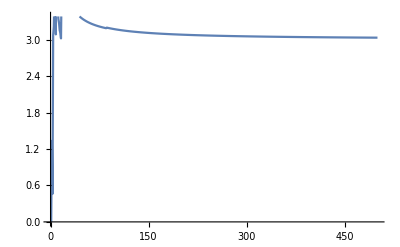

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
BooleanConvert[(a1&&a2&&a3)||(b1&&b2&&b3),"CNF"]
```

(a1||b1)&&(a1||b2)&&(a1||b3)&&(a2||b1)&&(a2||b2)&&(a2||b3)&&(a3||b1)&&(a3||b2)&&(a3||b3)

```mathematica
BooleanMinimize[((1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4))||(5&&6&&7)||(5&&6&&8)||(5&&7&&8)||(6&&7&&8)⧦((1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4))||((5||6)&&(5||7)&&(5||8)&&(6||7)&&(6||8)&&(7||8)),"CNF"]
```

True

```mathematica
BooleanConvert[(5&&6&&7)||(5&&6&&8)||(5&&7&&8)||(6&&7&&8),"CNF"]
```

(5||6)&&(5||7)&&(5||8)&&(6||7)&&(6||8)&&(7||8)

```mathematica
ltNew[x_,y_]:=Block[{len=Length[x]},And@@Flatten[Table[((atmost[y,n])⇒(atmost[x,n-1]))&&((atleast[x,m])⇒(atleast[y,m+1])),{n,1,len},{m,0,len}]]]
ltNew[{!a,!b,!c},{d,e,f}];
BooleanMinimize[%,"CNF"]//tolist//Column
```

a||b||c
a||b||d
a||b||e
a||b||f
a||c||d
a||c||e
a||c||f
a||d||e
a||d||f
a||e||f
b||c||d
b||c||e
b||c||f
b||d||e
b||d||f
b||e||f
c||d||e
c||d||f
c||e||f
d||e||f

```mathematica
BooleanConvert[(a&&b&&c)||(d&&e&&f)||(g&&h&&i),"CNF"]
```

(a||d||g)&&(a||d||h)&&(a||d||i)&&(a||e||g)&&(a||e||h)&&(a||e||i)&&(a||f||g)&&(a||f||h)&&(a||f||i)&&(b||d||g)&&(b||d||h)&&(b||d||i)&&(b||e||g)&&(b||e||h)&&(b||e||i)&&(b||f||g)&&(b||f||h)&&(b||f||i)&&(c||d||g)&&(c||d||h)&&(c||d||i)&&(c||e||g)&&(c||e||h)&&(c||e||i)&&(c||f||g)&&(c||f||h)&&(c||f||i)

```mathematica
A||B||C == ∀ a∈A,b∈B,c∈C,a&&b&&c
```

```mathematica
BooleanConvert[Exists[x,ForAll[x2,P[x,x2]]]||ForAll[y,Exists[y2,Q[y,y2]]],"CNF"]
```

∃_x∀_x2 P[x,x2]||∀_y∃_y2 Q[y,y2]

```mathematica
Range[1,3]
```

{1,2,3}

```mathematica
atmost[l_,n_]:=If[n≥Length[l],True,Or@@Map[Fold[And,True,Map[!#&,#]]&,Subsets[l,{Length[l]-n}]]]
atmost[{1,2,3,4},2]
BooleanMinimize[%,"CNF"]
Table[BooleanMinimize[atmost[Range[1,i],1],"CNF"],{i,1,5}]//Column
```

(!1&&!2)||(!1&&!3)||(!1&&!4)||(!2&&!3)||(!2&&!4)||(!3&&!4)

(!1||!2||!3)&&(!1||!2||!4)&&(!1||!3||!4)&&(!2||!3||!4)

True
!1||!2
(!1||!2)&&(!1||!3)&&(!2||!3)
(!1||!2)&&(!1||!3)&&(!1||!4)&&(!2||!3)&&(!2||!4)&&(!3||!4)
(!1||!2)&&(!1||!3)&&(!1||!4)&&(!1||!5)&&(!2||!3)&&(!2||!4)&&(!2||!5)&&(!3||!4)&&(!3||!5)&&(!4||!5)

```mathematica
BooleanMinimize[((a&&b&&c)⇒(d&&e&&f))&&((g&&h&&i)⇒(j&&k&&l)),"CNF"]
```

(!a||!b||!c||d)&&(!a||!b||!c||e)&&(!a||!b||!c||f)&&(!g||!h||!i||j)&&(!g||!h||!i||k)&&(!g||!h||!i||l)

```mathematica
nn=4;
onemin[x_,y_,n_]:=Block[{form=(atleast[x,n])⇒(atleast[y,n+1])},{form,BooleanConvert[form,"CNF"]}]
onemin[Map[!#&,Range[1,nn]],Range[nn+1,2nn],1]
tolist[Last[%]]//Column
```

{!1||!2||!3||!4⇒(5&&6)||(5&&7)||(5&&8)||(6&&7)||(6&&8)||(7&&8),(1||5||6||7)&&(1||5||6||8)&&(1||5||7||8)&&(1||6||7||8)&&(2||5||6||7)&&(2||5||6||8)&&(2||5||7||8)&&(2||6||7||8)&&(3||5||6||7)&&(3||5||6||8)&&(3||5||7||8)&&(3||6||7||8)&&(4||5||6||7)&&(4||5||6||8)&&(4||5||7||8)&&(4||6||7||8)}

1||5||6||7
1||5||6||8
1||5||7||8
1||6||7||8
2||5||6||7
2||5||6||8
2||5||7||8
2||6||7||8
3||5||6||7
3||5||6||8
3||5||7||8
3||6||7||8
4||5||6||7
4||5||6||8
4||5||7||8
4||6||7||8

```mathematica
"X<Y";
"(Requires |X|==|Y|)";
lt[x_,y_]:=Block[{len=Length[x]},
BooleanMinimize[(BooleanMinimize[And@@Table[(atleast[x,i])⇒(atleast[y,i+1]),{i,0,len}],"CNF"])&&(BooleanMinimize[And@@Table[(atmost[y,i])⇒(atmost[x,i-1]),{i,0,len}],"CNF"]),"CNF"]]
```

```mathematica
nn=2;
lt[Map[!#&,Range[1,nn]],Range[nn+1,2nn]]
tolist[%]//Column
```

(1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4)

1||2
1||3
1||4
2||3
2||4
3||4

```mathematica
BooleanConvert[(1||2)&&(1||3)&&(1||4)&&(2||3)&&(2||4)&&(3||4),"DNF"]
```

(1&&2&&3)||(1&&2&&4)||(1&&3&&4)||(2&&3&&4)

```mathematica
Subscript[a, 1]:=Subscript[α, 1,1]&&Subscript[α, 1,2]&&Subscript[α, 1,3]
Subscript[b, 1]:=¬Subscript[α, 1,1]&&¬Subscript[α, 1,2]&&¬Subscript[α, 1,3]
Subscript[b, 1]:=¬¬(¬Subscript[α, 1,1]&&¬Subscript[α, 1,2]&&¬Subscript[α, 1,3])
Subscript[b, 1]:=¬(Subscript[α, 1,1]||Subscript[α, 1,2]||Subscript[α, 1,3])
¬Subscript[b, 1]:=Subscript[α, 1,1]||Subscript[α, 1,2]||Subscript[α, 1,3]


Subscript[a, 1]:=Subscript[α, 1,1]∧Subscript[α, 1,2]∧Subscript[α, 1,3]
¬Subscript[b, 1]:=Subscript[α, 1,1]∨Subscript[α, 1,2]∨Subscript[α, 1,3]
```

```mathematica
{1,2}
{1,i,2};i∈[3,n]
```

```mathematica
"stuffed means that next must be longer";
stuffed[l_]:=last-first==len-1
```

```mathematica
"a:b:c:d →  (d not stuffed, increment d)
			c:d not stuffed, increment c
			b:c:d not stuffed, increment b
			a:b:c:d not stuffed, increment a
			else, all stuffed and -> [1..len]++[last]

d:c:b:a → d not stuffed, increment d

let stuffed l = (last l) - (head l) == (length l) - 1

if stuffed, [1..len]++[last l]
else,

D front back = if stuffed (reverse front) then D
```

```mathematica
rtups={{1},
{2},
{1,2},
{3},
{1,3},
{2,3},
{1,2,3},
{4},
{1,4},
{2,4},
{3,4},
{1,2,4},
{1,3,4},
{2,3,4},
{1,2,3,4},
{5},
{1,5},
{2,5},
{3,5},
{4,5},
{1,2,5},
{1,3,5},
{1,4,5},
{2,3,5},
{2,4,5},
{3,4,5},
{1,2,3,5},
{1,2,4,5},
{1,3,4,5},
{2,3,4,5},
{1,2,3,4,5},
{6},
{1,6},
{2,6},
{3,6},
{4,6},
{5,6},
{1,2,6},
{1,3,6},
{1,4,6},
{1,5,6},
{2,3,6},
{2,4,6},
{2,5,6},
{3,4,6},
{3,5,6},
{4,5,6},
{1,2,3,6},
{1,2,4,6},
{1,2,5,6},
{1,3,4,6},
{1,3,5,6},
{1,4,5,6},
{2,3,4,6},
{2,3,5,6},
{2,4,5,6},
{3,4,5,6},
{1,2,3,4,6},
{1,2,3,5,6},
{1,2,4,5,6},
{1,3,4,5,6},
{2,3,4,5,6},
{1,2,3,4,5,6}};
```

```mathematica
BooleanMinimize[(a1&&a2&&a3)||(a1||a2||a3),"CNF"]
```

a1||a2||a3

```mathematica
n=7;
Sort[Map[Drop[Drop[#,1],-1]&,FindPath[CompleteGraph[n],1,2,{3},All]]]//Column
```

{3,4}
{3,5}
{3,6}
{3,7}
{4,3}
{4,5}
{4,6}
{4,7}
{5,3}
{5,4}
{5,6}
{5,7}
{6,3}
{6,4}
{6,5}
{6,7}
{7,3}
{7,4}
{7,5}
{7,6}

```mathematica
n=4;
x=Map[toforms,FindPath[CompleteGraph[n],1,2,∞,All]]
y=Map[toforms,FindPath[CompleteGraph[n],2,1,∞,All]]
ltcnf[x,y]
```

{b_1&&a_1,b_4&&a_4&&b_5&&!a_5,b_2&&a_2&&b_3&&!a_3,b_4&&a_4&&b_6&&!a_6&&b_3&&!a_3,b_2&&a_2&&b_6&&a_6&&b_5&&!a_5}

{b_1&&!a_1,b_5&&a_5&&b_4&&!a_4,b_3&&a_3&&b_2&&!a_2,b_5&&a_5&&b_6&&!a_6&&b_2&&!a_2,b_3&&a_3&&b_6&&a_6&&b_4&&!a_4}

False

```mathematica
"i,j is i→j"
```

{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4}

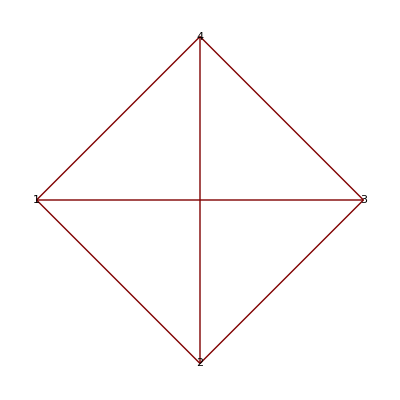

```mathematica
EdgeList[CompleteGraph[4]]
GraphPlot[Graph[%],VertexLabeling->True]
```

```mathematica
Normal[AdjacencyMatrix[Graph[{1->2,2->3,3->4,4->1,1->3,4->2}]]]//MatrixForm
```

(0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 1 | 0 | 0)

```mathematica
normedsum[vec_]:=Block[{tot=Total[vec]},If[tot>0,vec/tot,vec]]
normedsum[{0,0,1,0,1,1}]
```

{0,0,1/3,0,1/3,1/3}

```mathematica
tomarkov[mat_]:=Map[normedsum,mat]
Normal[AdjacencyMatrix[Graph[{1->2,2->3,3->4,4->1,1->3,4->2}]]]//MatrixForm
tomarkov[Normal[AdjacencyMatrix[Graph[{1->2,2->3,3->4,4->1,1->3,4->2}]]]]//MatrixForm
```

(0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 1 | 0 | 0)

(0 | 1/2 | 1/2 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1/2 | 1/2 | 0 | 0)

```mathematica
ExpMatPower[mat0_,n_]:=Block[{mat=mat0},Do[mat=mat.mat,{i,1,n}];mat]
```

```mathematica
Table[ExpMatPower[{{1,1},{1,0}},i]==MatrixPower[{{1,1},{1,0}},2^i],{i,1,5}]
```

{True,True,True,True,True}

```mathematica
ExpMatPower[tomarkov[AdjacencyMatrix[Graph[{1->2,2->3,3->4,4->1,1->3,4->2}]]],15]//N
```

{{0.153846,0.230769,0.307692,0.307692},{0.153846,0.230769,0.307692,0.307692},{0.153846,0.230769,0.307692,0.307692},{0.153846,0.230769,0.307692,0.307692}}

```mathematica
ExpGraph[g_,n_]:=Block[{exped=N[ExpMatPower[tomarkov[AdjacencyMatrix[g]],n]]},
Block[{m=Max[Flatten[exped]]},
AdjacencyGraph[Map[Piecewise[{{1, #≥m}, {0, #<m}}]&,exped,{2}]]]]
```

```mathematica
nthor[g_,n_]:=Block[{es=EdgeList[g],len=EdgeCount[g]},
Block[{v=PadLeft[IntegerDigits[n,2],len]},
Graph[Table[Piecewise[{{es[[i]][[1]]->es[[i]][[2]], v[[i]]==0}, {es[[i]][[2]]->es[[i]][[1]], True}}],{i,1,len}]]]]
```

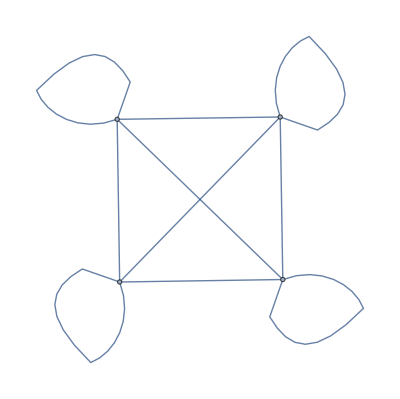
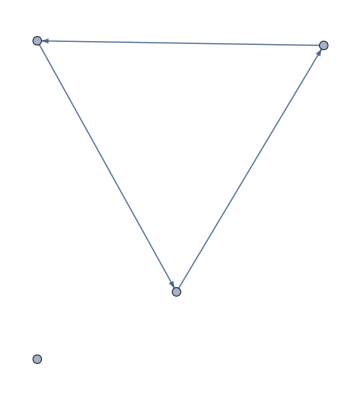
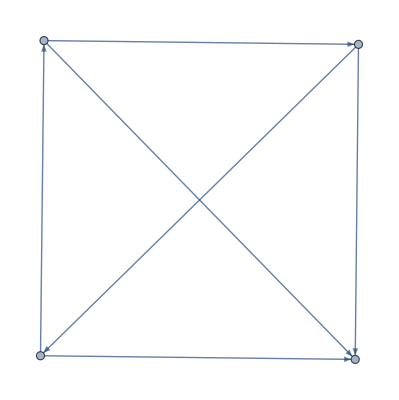
{{False,-Graphics-},{True,-Graphics-},{True,-Graphics-},{True,-Graphics-}}

```mathematica
DeleteDuplicates[Sort[Table[{Length[FindCycle[nthor[CompleteGraph[4],i],∞,3]]>0,ExpGraph[nthor[CompleteGraph[4],i],10]},{i,0,2^EdgeCount[CompleteGraph[4]]-1}]],#1[[1]]==#2[[1]]&&IsomorphicGraphQ[#1[[2]],#2[[2]]]&]
```

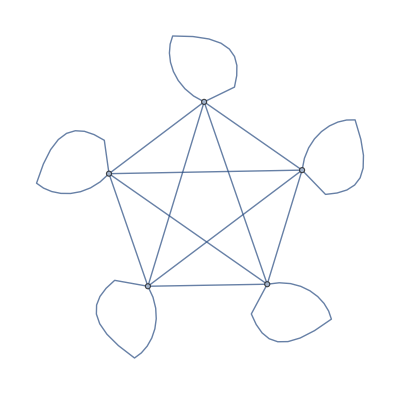
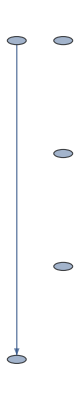
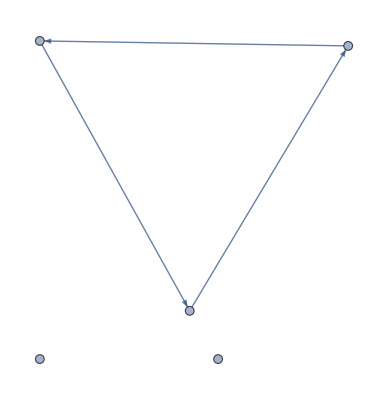
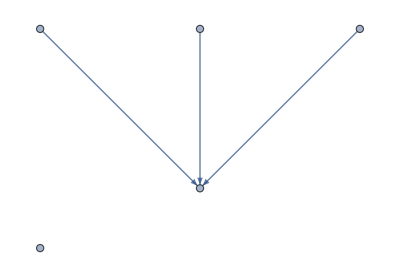
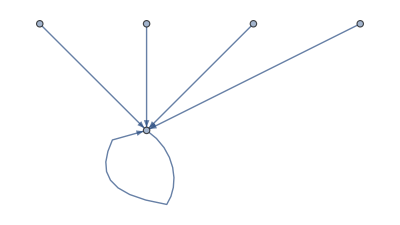
{{False,-Graphics-},{True,-Graphics-},{True,-Graphics-},{True,-Graphics-},{True,-Graphics-},{True,-Graphics-},{True,-Graphics-}}

```mathematica
DeleteDuplicates[Sort[Table[{Length[FindCycle[nthor[CompleteGraph[5],i],∞,3]]>0,ExpGraph[nthor[CompleteGraph[5],i],10]},{i,0,2^EdgeCount[CompleteGraph[5]]-1}]],#1[[1]]==#2[[1]]&&IsomorphicGraphQ[#1[[2]],#2[[2]]]&]
```

```mathematica
Simplify[Reduce[((a+b≤c+d)&&(b≥c))⇒(a≤d)],((a+b≤c+d)&&(b≤c))]
```

True

```mathematica
Simplify[Reduce[((a+b≤c+d)&&(a≥d))]]
```

(c|d)∈Reals&&a≥d&&a+b≤c+d

```mathematica
1,2
1,3
2,3
1,4
2,4
3,4
1,5
2,5
3,5
4,5
```

```mathematica
Flatten[Table[{i,j},{j,2,10},{i,1,j-1}],1]
FullSimplify[InterpolatingPolynomial[Table[{%[[i]],i},{i,1,Length[%]}],{a,b}]]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10}}

1+a+1/2 (-3+b) b

```mathematica
Map[Last,Flatten[Table[{i,j},{j,2,10},{i,1,j-1}],1]]
```

{2,3,3,4,4,4,5,5,5,5,6,6,6,6,6,7,7,7,7,7,7,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10}

```mathematica
Table[n-Floor[(-1+Sqrt[8*n-7])/2]*(Floor[(-1+Sqrt[8*n-7])/2]+1)/2,{n,1,10}]
```

{1,1,2,1,2,3,1,2,3,4}

```mathematica
FullSimplify[i-Floor[(-1+Sqrt[8*i-7])/2]*(Floor[(-1+Sqrt[8*i-7])/2]+1)/2,i≥1&&Element[i,Integers]]
```

i-1/2 Floor[1/2 (-1+√(-7+8 i))] (1+Floor[1/2 (-1+√(-7+8 i))])

```mathematica
Table[Ceiling[(Sqrt[8(n+1)-7]+1)/2],{n,1,10}]
```

{2,3,3,4,4,4,5,5,5,5}

```mathematica
FullSimplify[Ceiling[(Sqrt[8(i+1)-7]+1)/2],i≥1&&Element[i,Integers]]
```

Ceiling[1/2 (1+√(1+8 i))]

```mathematica
Expand[1+(i-1/2 Floor[1/2 (-1+√(-7+8 i))] (1+Floor[1/2 (-1+√(-7+8 i))]))+1/2 (-3+Ceiling[1/2 (1+√(1+8 i))]) Ceiling[1/2 (1+√(1+8 i))]]
```

1+i-3/2 Ceiling[1/2 (1+√(1+8 i))]+1/2 Ceiling[1/2 (1+√(1+8 i))]^2-1/2 Floor[1/2 (-1+√(-7+8 i))]-1/2 Floor[1/2 (-1+√(-7+8 i))]^2

```mathematica
Reduce[{x≤√y≤x+2,x≥0,y≥0},y,Integers]
```

(x|y)∈Integers&&x≥0&&x^2≤y≤4+4 x+x^2

```mathematica
Expand[(2b-1)^2+4(2b-1)+4]
```

1+4 b+4 b^2

```mathematica
Expand[(2c+1)^2+4(2c+1)+4+7]
```

16+12 c+4 c^2

```mathematica
Expand[c(1+c)]
```

c+c^2

```mathematica
Expand[b(b-3)]
```

-3 b+b^2

```mathematica
Expand[(2i+2)(2i-2b)/4]
```

-b+i-b i+i^2

```mathematica
Reduce[{2≠b c(1+c)(b-3),
b≤1/2(1+√(8i+1))≤b+1,
1/2(1+√(8i+1))-1<b≤1/2(1+√(8i+1)),
c≤1/2(-1+√(8i-7))≤c+1,
1/2(-1+√(8i-7))<c≤1/2(-1+√(8i-7)),i≥1},Integers]
```

False

```mathematica
BooleanConvert[(a&&b&&x)||(!a&&b&&y)||(!b),"CNF"]
```

(!a||!b||x)&&(a||!b||y)

```mathematica
BooleanConvert[(!a||!b||c1||c2)&&(!a||!b||c1||c3)&&(!a||!b||c2||c3)&&
(a||!b||d1)&&(a||!b||d2)&&(a||!b||d3),"CNF"]
```

(!a||!b||c1||c2)&&(!a||!b||c1||c3)&&(!a||!b||c2||c3)&&(a||!b||d1)&&(a||!b||d2)&&(a||!b||d3)

```mathematica
ρ[b1&&Forall[a,a∈a1⇒a]]==b1&&ForAll[a,a∈a1⇒!a]
```

ρ[b1&&Forall[a,a∈a1⇒a]]==b1&&∀_a(a∈a1⇒!a)